```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/sarp/Desktop/Binary_NS_detection_Work

SETTING UP

## LIGO L1,H1 STRAIN during GW170817

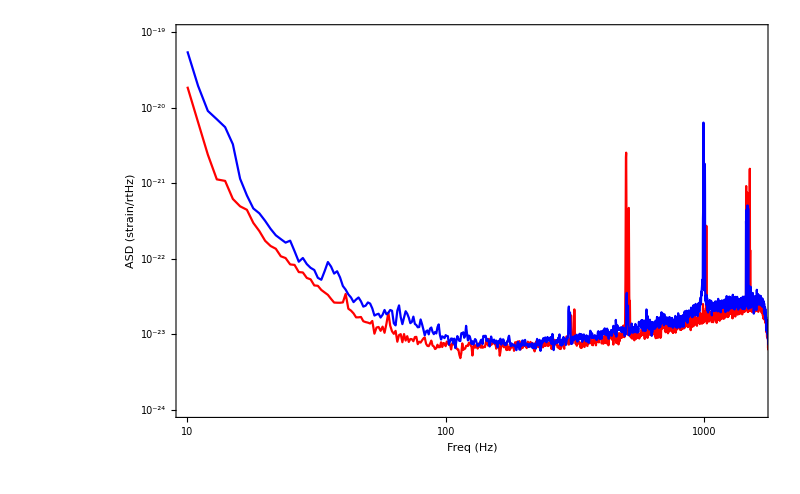

```mathematica
L1data="L-L1_LOSC_CLN_4_V1-1187007040-2048.hdf5";
H1data="H-H1_LOSC_CLN_4_V1-1187007040-2048.hdf5";
L1strain=SetPrecision[Import[L1data,{"Datasets","/strain/Strain"}],16];
H1strain=SetPrecision[Import[H1data,{"Datasets","/strain/Strain"}],16];
dt=1/4096;
(*L1attributes=Import[L1data,{"Attributes","/strain/Strain"}]
{t0,dtfloat,n}={"Xstart","Xspacing","Npoints"}/.L1attributes

dt-dtfloat
time=t0+(Range[n]-1) dt;*)
HannWindowTable=Table[HannWindow[(i-2048.5`16)/4096],{i,1,4096}];
MeanHann=Mean[Abs[Fourier[HannWindowTable]]^2];
AOL1specHann=Mean[Table[Abs[Fourier[L1strain[[1+4096 n;;4096 (n+1)]] HannWindowTable]]^2,{n,0,31}]]/MeanHann;
AOH1specHann=Mean[Table[Abs[Fourier[H1strain[[1+4096 n;;4096 (n+1)]] HannWindowTable]]^2,{n,0,31}]]/MeanHann;
L1ASD=Table[{i,Sqrt[2 dt AOL1specHann[[i+1]]]},{i,10,2000}];
H1ASD=Table[{i,Sqrt[2 dt AOH1specHann[[i+1]]]},{i,10,2000}];
GW170817L1ASDPlot=ListLogLogPlot[{L1ASD,H1ASD},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Red,Blue},FrameLabel->{"Freq (Hz)","ASD (strain/rtHz)"},PlotRange->{{10,1600},{10^-24,10^-19}},ImageSize->800]
```

## INTERPOLATING L1, H1 GW170817 ASD and REMOVING BUMPS (not done)

```mathematica
L1ASDfit=Interpolation[L1ASD];
H1ASDfit=Interpolation[L1ASD];
```

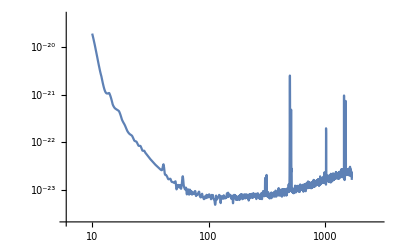

```mathematica
LogLogPlot[L1ASDfit[x],{x,10,1700}]
```

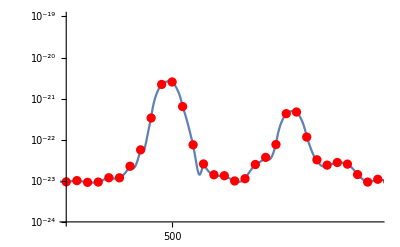

```mathematica
Show[LogLogPlot[L1ASDfit[x],{x,400,600},PlotRange->{{490,520},{10^-24,10^-19}}],ListLogLogPlot[L1ASD[[470;;520]],Frame->True,PlotStyle->{Red},FrameLabel->{"Freq (Hz)","ASD (strain/rtHz)"}]]
```

## DATA from A-LIGO BNS Optimized, Einstein Telescope B Low-frequency end

#### ASD = 2 h̃(f) √f where h̃(f) is the Fourier transform of h(t)

```mathematica
ALIGO2017Data={{7*10^5,6000,100,20,4,2,1,0.9,0.8,0.9,1,2,4}*10^-23,{9,10,15,20,30,40,70,80,100,200,400,1000,1200}};
ALIGODesigndata={{10^5,10^4,100,32,20,8,5,2.35,1,0.6,0.4,0.3,0.25,0.3,0.8,3}*10^-23,{6,7,9,9.7,10,11.89,14,20,30,40,60,200,300,400,900,1200}};
ETdata={{10^6,500,(*50,40,20,*)14,6,3,2,1,0.5,0.15,0.06,0.03,0.025,0.03,0.07,0.13,0.2}*10^-23,{0.5,1,(*1.2,1.3,1.5,*)2,3,4,5,7,10,20,30,60,150,300,1000,2000,3000}};
data={ALIGO2017Data,ALIGODesigndata,ETdata};
choice=3;
Ls=Table[Length[data[[i,1]]],{i,1,3}]
```

{13,16,16}

```mathematica
ThreeIFOData=Table[{data[[j,2,i]],data[[j,1,i]]},{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
GWFreqs=Table[ThreeIFOData[[j,i,1]],{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
ASDData=Table[ThreeIFOData[[j,i,2]],{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
ASDvFreqData=Table[{GWFreqs[[j,i]],ASDData[[j,i]]},{j,1,Length[data]},{i,1,Ls[[j]]}];
```

## BETTER ASD DATA using ONLINE SOFTWAREWebPlotDigitizer

### Jocelyn Read’s Realistic BNS Inspiral DATA

```mathematica
ReadBNSData=Import["BNS_data_Read.csv","Data"];
RealisticBNSData=Sort[ReadBNSData];
```

### EXTRA ET DATA

```mathematica
ExtraETCData={{1.1388108937271446,9.609459526468317 10^-22},{1.1529964151058092,7.8114842961191475 10^-22},{1.1892381077160423,5.957808026448449 10^-22},{1.2190499622963578,4.999907130470519 10^-22}};

NewETBdata={{1.167358637478373,8.944521110882274 10^-22},{1.1892381077160423,7.446845066646906 10^-22},{1.2266189715032598,5.863623678813286 10^-22},{1.2651748135966814,4.96022903404055 10^-22}};
```

### A-LIGO DESIGN, ET-B, ET-C DATA

```mathematica
TextSize=22;
ALIGO2020Data=Join[{ASDvFreqData[[2,1]]},{ASDvFreqData[[2,3]]},Sort[Import["ALIGO2020.csv","Data"]]];
ETBData=Join[NewETBdata,Drop[Sort[Import["ET_B.csv","Data"]],{1,5}]](*Sort[Import["ET_B.csv","Data"]]*);
ETCData=Join[ExtraETCData,Drop[Sort[Import["ET_C.csv","Data"]],{1}]](*Sort[Import["ET_C.csv","Data"]]*);
```

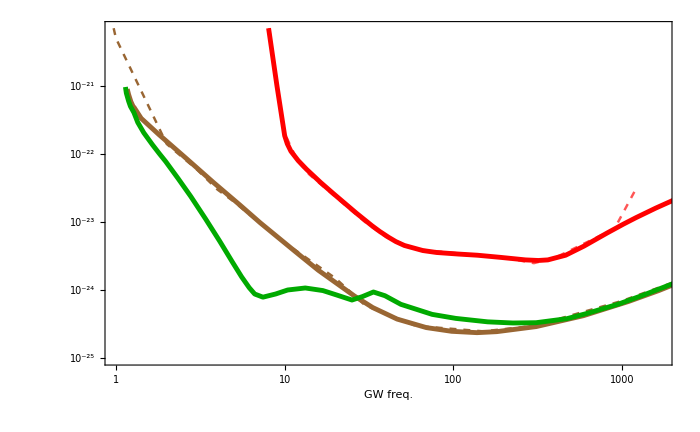

```mathematica
IFOASDs=ListLogLogPlot[{ASDvFreqData[[2]],ASDvFreqData[[3]],ALIGO2020Data,ETBData,ETCData},PlotRange->{{1,1700},{10^-25,7 10^-21}},Joined->True,PlotStyle->{Directive[{Thickness[0.0025],Dashed,Lighter[Red]}],{Thickness[0.0025],Dashed,Brown},{Thickness[0.005],Red},{Thickness[0.005],Brown},{Thickness[0.005],Darker[Green]}},AxesLabel->{"GW freq.",None},ImageSize->700,Frame->True,FrameStyle->Thick,FrameTicksStyle->24,Epilog->Inset[Framed[Column[{LineLegend[{Directive[{Thickness[0.008],Dashed,Lighter[Red]}],{Thickness[0.008],Dashed,Brown},{Thickness[0.0125],Red},{Thickness[0.0125],Brown},{Thickness[0.0125],Darker[Green]}},{Style["Old A-LIGO2020 Data",TextSize],Style["Old ET-B Data",TextSize],Style["New A-LIGO2020",TextSize],Style["New ET-B",TextSize],Style["ET-C",TextSize]}]}],RoundingRadius->5,FrameStyle->Directive[Black,AbsoluteThickness[4]],Background->White],Scaled[{0.75,0.75}]]]
(*Export["Figures/All_IFO_strains.pdf",IFOASDs]*)
```

## Preliminaries

```mathematica
Clear[x,h]
```

```mathematica
X=(G M Ω/c^3)^(2/3);
Msun=1.989*10^30;
clight=299792458;
Ggrav=6.67*10^-11;
ν=1/4;
Mc=ν^(3/5)M;
fISCO=c^3/(6^(3/2)π G M);
AngAveFact=1/Pi Integrate[(1+Cos[i]^2)/2,{i,0,Pi}];
Mpc=10^6*360/(2π)*3600*149597870700.;
GWfreqIsco=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},fISCO]
fISCOGW170817=Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},fISCO]
Mtot=2.8 Msun;
```

1570.97

1605.37

## MERGER RATES

```mathematica
R={1540,1540+3200,1540-1220}
```

{1540,4740,320}

```mathematica
R*(40./1000)^3
```

{0.09856,0.30336,0.02048}

## AVERAGING of the ANTENNA PATTERNS

```mathematica
InclinationAv=1/2 Integrate[(((1+Cos[i]^2)/2)^2+Cos[i]^2)Sin[i],{i,0,-Pi,Pi}]
```

4/5

```mathematica
Fplus=1/2(1+Cos[θ]^2)Cos[2ϕ]Cos[2ψ]-Cos[θ]Sin[2ϕ]Sin[2ψ];
Fx=1/2(1+Cos[θ]^2)Cos[2ϕ]Sin[2ψ]+Cos[θ]Sin[2ϕ]Cos[2ψ];
```

```mathematica
Fplus/.ψ->0/.ϕ->0/.θ->0
```

1

```mathematica
(*Average over θ,ϕ,ψ*)
1/(8 Pi^2)Integrate[Fplus^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
1/(8 Pi^2)Integrate[Fx^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
LowAv=√(1/5 InclinationAv)
```

1/5

1/5

2/5

```mathematica
(*Set ψ=0, average over θ,ϕ*)
1/(4Pi)Integrate[Fplus^2*Sin[θ]/.ψ->0,{θ,0,Pi},{ϕ,0,2π}]
1/(4Pi)Integrate[Fx^2*Sin[θ]/.ψ->0,{θ,0,Pi},{ϕ,0,2π}]
MedAv=√(7/30+1/6)
```

7/30

1/6

√(2/5)

## ATTEMPT TO COMPUTE ANGULAR STANDARD DEVIATION

```mathematica
t1=1/(8 Pi^2)Integrate[Cos[θ] ϕ ψ Fplus^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
t2=1/(8 Pi^2)Integrate[Cos[θ] ϕ ψ Fx^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
```

-1/120

1/120

```mathematica
t1*1/2 Integrate[(((1+Cos[i]^2)/2)^2-Cos[i]^2)Cos[i]Sin[i],{i,0,-Pi,Pi}]
```

0

```mathematica
t1=1/(8 Pi^2)Integrate[(Cos[θ] ϕ ψ )^2 Fplus^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
t2=1/(8 Pi^2)Integrate[(Cos[θ] ϕ ψ)^2 Fx^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
```

(99+96 π^2+11264 π^4)/60480

(11 (-9+1024 π^4))/60480

```mathematica
EX2=1/(8 Pi^2)1/2 1/2 Integrate[(t1((1+Cos[i]^2)/2)^2-t2 Cos[i]^2)Cos[i]^2 Sin[i],{i,0,-Pi,Pi}]
```

(1089+552 π^2+5632 π^4)/(25401600 π^2)

```mathematica
√(1. EX2)
```

0.0470568

## FREQ-DOMAIN STRAINS

```mathematica
A=π^(-2/3)√(5/24);
hFDOld[f_,D_]=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},AngAveFact*A*√2 c/D(G Mc/c^3)^(5/6)f^(-7/6)];
hFDHigh[f_,D_]=Block[{G=6.67*10^-11,(*M=(2.8Msun),*)c=clight}, 2LowAv A c/D(G Mc/c^3)^(5/6)f^(-7/6)]
hFDMed[f_,D_]=Block[{G=6.67*10^-11,(*M=(2.8Msun),*)c=clight},MedAv A c/D(G Mc/c^3)^(5/6)f^(-7/6)]
hFDRMS[f_,D_]=Block[{G=6.67*10^-11,(*M=(2.8Msun),*)c=clight},LowAv A c/D(G Mc/c^3)^(5/6)f^(-7/6)]
hFDVeryLow[f_,D_]=Block[{G=6.67*10^-11,(*M=(2.8Msun),*)c=clight},(2LowAv-MedAv) A c/D(G Mc/c^3)^(5/6)f^(-7/6)]
```

(5.431×10^-23 M^(5/6))/(D f^(7/6))

(4.29358×10^-23 M^(5/6))/(D f^(7/6))

(2.7155×10^-23 M^(5/6))/(D f^(7/6))

(1.13742×10^-23 M^(5/6))/(D f^(7/6))

## LIGO2017 COMPARISON

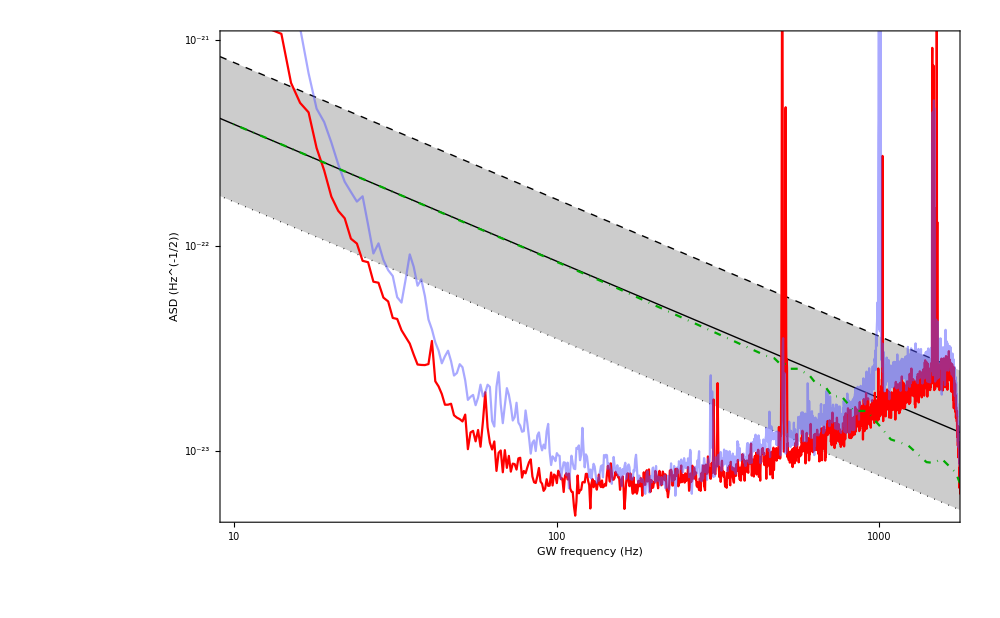

```mathematica
TextSize=22;
Block[{M=2.74Msun},FigGW170817=Show[LogLogPlot[{2 √f hFDHigh[f,40Mpc],(*2 √f hFDMed[f,40Mpc],*)2 √f hFDRMS[f,40Mpc],2 √f hFDVeryLow[f,40Mpc]},{f,1,2000},PlotStyle->{(*{Gray,Opacity[0.2]},*){Black,Dashed,Thick},{Thick,Black},{Black,Dotted,Thick},{Gray,Opacity[0]}},
Filling->{1->{3}}(*},{2->{4}}}*),FillingStyle->{{Directive[Black,Opacity[0.25]]}},PlotRange->{{10,fISCOGW170817},{5 10^-24,10^-21}}],
(*Graphics[Line[{{Log[fISCOGW170817],Log[10^-24]},{Log[fISCOGW170817],Log[10^-21]}}]],*) (* plots ISCO vertically *)
ListLogLogPlot[{L1ASD,H1ASD,1.01RealisticBNSData},Joined->True,PlotStyle->{Red,{Lighter[Blue],Opacity[0.5]},{DotDashed,Darker[Green]}},AxesLabel->{"GW freq.",None},PlotRange->{All,All}],ImageSize->1000,
Frame->True,FrameStyle->Directive[Black,24,AbsoluteThickness[3]],FrameLabel->{Style["GW frequency (Hz)",24],Style["ASD (Hz^(-1/2))",24]},ImageSize->1000,Epilog->Inset[Framed[Column[{LineLegend[{Directive[Red,AbsoluteThickness[3]],Directive[Lighter[Blue],Thickness[0.01],Opacity[0.5]],Directive[Black,Dashing[0.025],Thickness[0.01]],Directive[Black,Thickness[0.01]],Directive[Black,Dotted,Thickness[0.01]]},{Style["L1 during GW170817",TextSize],Style["H1 during GW170817",TextSize],Style["2√f(H̃)_h(f)",TextSize],Style["2√f(H̃)_m(f)",TextSize],Style["2√f(H̃)_l(f)",TextSize]}]}],RoundingRadius->5,FrameStyle->Directive[Black,AbsoluteThickness[4]],Background->White],Scaled[{0.8375,0.8375}]],FrameTicks->{{{{Log[10^-21],"10^-21"},{Log[10^-22],"10^-22"},{Log[10^-23],"10^-23"},{Log[5 10^-22],"5x10^-21"},{Log[5 10^-23],"5x10^-23"}},None},{{{Log[10],"10"},{Log[50],"50"},{Log[100],"100"},{Log[500],"500"},{Log[1000],"1000"}},None}},FrameTicksStyle->24]]
(*Export["Figures/GW170817_strains.pdf",FigGW170817]*)
```

## DEFINE THE SNR

### INTERPOLATE ASD DATA: use low InterpOrd to avoid waviness in the fits

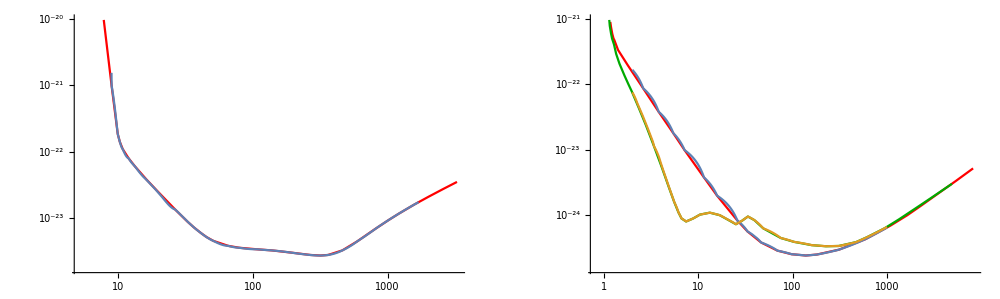

```mathematica
Snoise={Interpolation[ALIGO2020Data,InterpolationOrder->2],
Interpolation[ETBData,InterpolationOrder->1],Interpolation[ETCData,InterpolationOrder->1]};
GraphicsRow[{Show[ListLogLogPlot[ALIGO2020Data,Joined->True,PlotStyle->Red],LogLogPlot[Snoise[[1]][x],{x,6,1700}]],Show[ListLogLogPlot[{ETBData,ETCData},Joined->True,PlotStyle->{Red,Darker[Green]}],LogLogPlot[{Snoise[[2]][x],Snoise[[3]][x]},{x,2,1000}]]},ImageSize->1000]
```

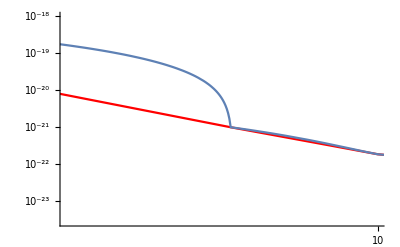

```mathematica
Show[ListLogLogPlot[ALIGO2020Data,Joined->True,PlotStyle->Red],LogLogPlot[Snoise[[1]][x],{x,6,100}],PlotRange->{{Log[8],Log[10]},Automatic}]
```

### CONSTRUCT the SNR

```mathematica
SNR2017High[fi_,ff_,D_]:=(NIntegrate[4 hFDHigh[f,D]^2/(L1ASDfit[f])^2,{f,fi,ff}])^(1/2)
SNR2017Med[fi_,ff_,D_]:=(NIntegrate[4 hFDMed[f,D]^2/(L1ASDfit[f])^2,{f,fi,ff}])^(1/2)
SNR2017RMS[fi_,ff_,D_]:=(NIntegrate[4 hFDRMS[f,D]^2/(L1ASDfit[f])^2,{f,fi,ff}])^(1/2)
SNR2017VeryLow[fi_,ff_,D_]:=(NIntegrate[4 (2hFDRMS[f,D]-hFDMed[f,D])^2/(L1ASDfit[f])^2,{f,fi,ff}])^(1/2)
SNRMax[i_,fi_,ff_,D_]:=(NIntegrate[4 hFDHigh[f,D]^2/(Snoise[[i]][f])^2,{f,fi,ff}])^(1/2)
SNR65[i_,fi_,ff_,D_]:=(NIntegrate[4 hFDMed[f,D]^2/(Snoise[[i]][f])^2,{f,fi,ff}])^(1/2) (* 65% of max *)
SNRRMS[i_,fi_,ff_,D_]:=(NIntegrate[4 hFDRMS[f,D]^2/(Snoise[[i]][f])^2,{f,fi,ff}])^(1/2)
SNRLow[i_,fi_,ff_,D_]:=(NIntegrate[4 (2hFDRMS[f,D]-hFDMed[f,D])^2/(Snoise[[i]][f])^2,{f,fi,ff}])^(1/2)
```

## Inspiral time, accumulated phase: 0PN to 3.5PN expressions

```mathematica
Tinsp0PN[f0_,Mch_]=5/(256 π^(8/3))  (c^3/(G Mch))^(5/3) f0^(-8/3)/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;
Phi0PN[f0_,Mch_,M_]=2 (5 G Mch/c^3)^(-5/8) Tinsp0PN[f0,Mch]^(5/8)/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;
Ncycles0PN[f0_,Mch_,M_]=1/(32 π^(8/3)) (G Mch/c^3)^(-5/3) (f0^(-5/3)-fISCO^(-5/3))/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;

(*2PN expressions from Section 5.6.4 of Maggiore's Book*)

τ0[f_,M_]:=5/(256 ν f π) (π G M/c^3 f)^(-5/3)/.G->6.67*10^-11/.c->clight;
τ1[f_,M_]:=5/(192 ν f π) (π G M/c^3 f)^-1 (743/336+11/4 ν)/.G->6.67*10^-11/.c->clight;
τ15[f_,M_]:=1/(8 ν f) (π G M/c^3 f)^(-2/3)/.G->6.67*10^-11/.c->clight;
τ2[f_,M_]:=5/(128 ν f π) (π G M/c^3 f)^(-1/3) (3058673/1016064+5429/1008 ν+617/144 ν^2)/.G->6.67*10^-11/.c->clight;


Tinsp2PN[f_,fin_,M_]:=τ0[fin,M] (1-(f/fin)^(-8/3))+τ1[fin,M] (1-(f/fin)^-2)-τ15[fin,M] (1-(f/fin)^(-5/3))+τ2[fin,M] (1-(f/fin)^(-4/3));
Phi2PN[f_,fin_,M_]:=16 π/5 fin (τ0[fin,M] (1-(f/fin)^(-5/3))+5/4 τ1[fin,M] (1-(f/fin)^-1)-25/16 τ15[fin,M] (1-(f/fin)^(-2/3))+5/2 τ2[fin,M] (1-(f/fin)^(-1/3)));
```

### 2+ PN from Blanchet’s Review Article

```mathematica
(* 3.5 PN non-spinning binary phase *)
K=SeriesCoefficient[X/.Ω-> π f,{f,0,2/3}];
Xvar[f_]=K f^(2/3);
(* x0 is an integration constant *)
phi[x_,x0_]=-x^(-5/2)/(32ν)(1+(3715/1008+55/12 ν)x-10 π x^(3/2)+(15293365/1016064+27145/1008 ν+3085/144 ν^2)x^2+(38645/1344-65/16 ν)π x^(5/2)Log[x/x0]+(12348611926451/18776862720-160/3 π^2-1712/21 EulerGamma-856/21 Log[16x]+(-15737765635/12192768+2255/48 π^2)ν+76055/6912 ν^2-127825/5184 ν^3)x^3+(77096675/2032128+378515/12096 ν-74045/6048 ν^2)π x^(7/2));
(* Accumulated phase from x1 to x2 = Φ[x1] - Φ[x2] *)
PhiAcc[x1_,x2_]=FullSimplify[phi[x1,x0]-phi[x2,x0]]/.Log[x1/x0]-Log[x2/x0]->Log[x1/x2];
```

### SOLVING x(Θ) = x(f=30Hz) for Θ gives us inspiral time

```mathematica
Clear[T]
(* Θ is a rescaled time variable where Δt = Subscript[t, coal]- t *)
Θ=ν c^3/(G M)(Δt)/5;
xoft[T_]=(1/4)T^(-1/4)(1+(743/4032+11/48 ν)T^(-1/4)-1/5 π T^(-3/8)+(19583/254016+24401/193536 ν+31/288 ν^2)T^(-1/2)+(-11891/53760+109/1920 ν)π T^(-5/8)+(-10052469856691/6008596070400+1/6 π^2+107/420 EulerGamma-107/3360 Log[T/256]+(3147553127/780337152-451/3072 π^2)ν-15211/442368 ν^2+25565/331776 ν^3)T^(-3/4)+(-113868647/433520640-31821/143360 ν+294941/3870720 ν^2)π T^(-7/8));
```

## CHECKS: GW170817 at LIGO 2017, use M = 2.74 M_Sun Swept from 30 Hz to~2000 Hz in 60 seconds and~3000 cycles with SNR=28.8 at L1

```mathematica
fin=30;
Th=Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},Θ];
xin=Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin==0,{Δt,50}][[1,2]];
Ncyc3p5PN=-1/Pi Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},PhiAcc[Xvar[fin],Xvar[fISCOGW170817]]];
Ncyc2PN=Phi2PN[fISCOGW170817,fin,2.74Msun]/(2Pi);
Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOGW170817,fin,2.74Msun], "(2PN) ", Tinsp0PN[fin,1.188Msun] ,"(0 PN) "," seconds"]
Print["𝒩_cycles  = ",Ncyc3p5PN"(3.5 PN), ",Ncyc2PN"(2PN), ",Ncycles0PN[fin,1.188Msun,2.74Msun] ,"(0PN)"]
```

τ_insp = 56.6472(3.5PN), 56.7156(2PN) 55.9091(0 PN)  seconds

𝒩_cycles  = 2710.62 (3.5 PN), 2718.29 (2PN), 2680.1(0PN)

```mathematica
SNRhigh2017=Block[{M=2.74Msun},SNR2017High[fin,fISCOGW170817,40 Mpc]]//Quiet;
SNRmed2017=Block[{M=2.74Msun},SNR2017Med[fin,fISCOGW170817,40 Mpc]]//Quiet;
SNRRMS2017=Block[{M=2.74Msun},SNR2017RMS[fin,fISCOGW170817,40 Mpc]]//Quiet;
SNRverylow2017=Block[{M=2.74Msun},SNR2017VeryLow[fin,fISCOGW170817,40 Mpc]]//Quiet;
Print["SNR(30Hz -> f_ISCO): ρ_h = ",SNRhigh2017," (optimal orientation), ρ_m= ",SNRRMS2017,"(RMS average), ρ_l = ",SNRverylow2017," (1σ from RMS)"]
ρtotGW170817=√(SNRhigh2017^2+0 SNRverylow2017^2+SNRRMS2017^2);
Print["ρ_tot = ",ρtotGW170817," (3 IFOs)" ](* vs. ", √(SNRhigh2017^2), "  (using Subscript[ρ, virgo] = 2 instead of Subscript[ρ, l])"]*)
```

SNR(30Hz -> f_ISCO): ρ_h = 28.6731 (optimal orientation), ρ_m= 14.3366(RMS average), ρ_l = 6.00503 (1σ from RMS)

ρ_tot = 32.0575 (3 IFOs)

ADVANCED-LIGO-VIRGO NETWORK

## PLOT: A-LIGO-VIRGO NETWORK 2020 and SOURCES

### A-LIGO PLOT

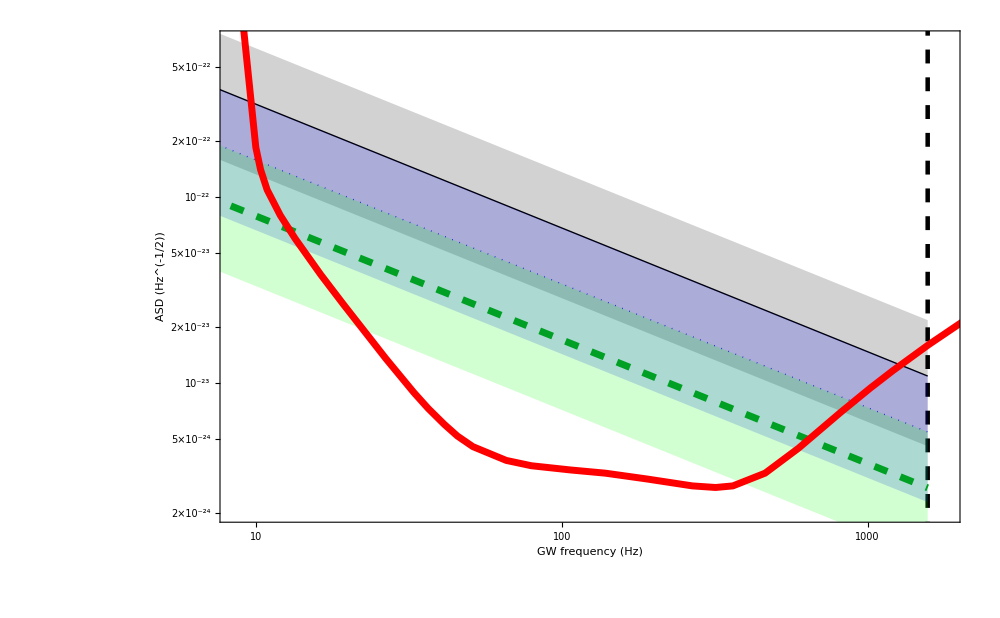

```mathematica
LIGOASDPlot=Block[{M=2.8Msun},Show[
LogLogPlot[{2 √f hFDRMS[f,50Mpc],2 √f hFDRMS[f,100Mpc],2 √f hFDRMS[f,200Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Black,Thick},{Blue,Dotted,Thick},{Darker[Green],Thickness[0.005],Dashing[0.01]}},PlotRange->{{8.5,1800},{2 10^-24, 7 10^-22}}],
LogLogPlot[{2 √f hFDHigh[f,50Mpc],2 √f hFDVeryLow[f,50Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},Filling->{1->{2}},FillingStyle->Directive[{Black,Opacity[0.175]}]],
LogLogPlot[{2 √f hFDHigh[f,100Mpc],2 √f hFDVeryLow[f,100Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Blue,Opacity[0]},{Blue,Opacity[0]}},Filling->{1->{2}},FillingStyle->Directive[{Blue,Opacity[0.175]}]],
LogLogPlot[{2 √f hFDHigh[f,200Mpc],2 √f hFDVeryLow[f,200Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Green,Opacity[0]},{Green,Opacity[0]}},Filling->{1->{2}},FillingStyle->Directive[{Green,Opacity[0.175]}]],
Graphics[{Black,Thickness[0.00325],Dashing[0.01],Line[{{Log[GWfreqIsco],Log[10^-25]},{Log[GWfreqIsco],Log[10^-20]}}]}],ListLogLogPlot[{ALIGO2020Data(*,8.95/10 RealisticBNSData*)},Joined->True,PlotStyle->{{Thickness[0.005],Red},{DotDashed,Thickness[0.0025],Opacity[0.75],Black}},AxesLabel->{"GW freq.",None}],ImageSize->1000,Frame->True,
FrameStyle->Directive[Black,24,AbsoluteThickness[3]],FrameLabel->{Style["GW frequency (Hz)",24],Style["ASD (Hz^(-1/2))",24]},
FrameTicks->{{{{Log[10^-21],"10^-21"},{Log[10^-22],"10^-22"},{Log[10^-23],"10^-23"},{Log[ 10^-24],"10^-24"},{Log[5 10^-23],"5x10^-23"},{Log[5 10^-22],"5x10^-22"},{Log[5 10^-24],"5x10^-24"}},None},{{{Log[2],"2"},{Log[5],"5"},{Log[10],"10"},{Log[20],"20"},{Log[50],"50"},{Log[100],"100"},{Log[200],"200"},{Log[500],"500"},{Log[1000],"1000"},{Log[GWfreqIsco],"f_ISCO"}},None}},FrameTicksStyle->24,
GridLines->{{Log[10],Log[20],Log[50],Log[100],Log[200],Log[500],Log[1000]},{Log[10^-23],Log[10^-22]}},
Epilog->Inset[Framed[Column[{
(*PointLegend[Directive[Black],Style["test",20],LegendMarkers->legmarkers],*)LineLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Black,Thickness[0.009]],Directive[Blue,Dotted,Thickness[0.007]],Directive[Darker[Green],Thickness[0.009],Dashing[0.02]]},{Style["A-LIGO 2020",TextSize],Style["BNS at 50 Mpc",TextSize],Style["BNS at 100 Mpc",TextSize],Style["BNS at 200 Mpc",TextSize]},LegendMarkerSize->{30,10}]}],RoundingRadius->5,Background->White],Scaled[{0.87,0.88}]]]]
(*Export["Figures/ALigo_strains.pdf",LIGOASDPlot];*)
```

## A-LIGO 2020 Advance Warning Times, D=40, 50, 100,200 Mpc

### A-LIGO entry frequencies f_0 for all 3 IFOs and and 4 sources

```mathematica
f0RootFinder[D_,fh_,fRMS_,fl_]:=Block[{M=2.8Msun},{2 √fh hFDHigh[fh,D]-Snoise[[1]][fh],2 √fRMS hFDRMS[fRMS,D]-Snoise[[1]][fRMS],2 √fl hFDVeryLow[fl,D]-Snoise[[1]][fl]}]
```

### Galactic BNS

```mathematica
aa=FindRoot[f0RootFinder[0.01Mpc,f1,f2,f3],{{f1,5},{f2,5},{f3,5}}][[All,2]]
```

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{142672.,2.83015,6.14093}

```mathematica
fbar=9.0023;
Block[{f=fbar,D=0.1Mpc,M=2.8Msun},(SNRMax[1,aa[[1]],f,D]^2+SNRRMS[1,aa[[2]],f,D]^2+SNRLow[1,aa[[3]],f,D]^2)^(1/2)]
fin=6;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]]/60
```

15.034

65.9645

```mathematica
f0={FindRoot[f0RootFinder[40Mpc,f1,f2,f3],{{f1,7},{f2,7},{f3,10}}][[All,2]],
FindRoot[f0RootFinder[50Mpc,f1,f2,f3],{{f1,10},{f2,10},{f3,10}}][[All,2]],FindRoot[f0RootFinder[100Mpc,f1,f2,f3],{{f1,10},{f2,10},{f3,10}}][[All,2]],
FindRoot[f0RootFinder[200Mpc,f1,f2,f3],{{f1,10},{f2,10},{f3,10}}][[All,2]]}
```

{{9.12479,9.5746,10.154},{9.28298,9.69963,10.5067},{9.69963,10.2202,14.0877},{10.2202,12.7318,21.7559}}

```mathematica
f0RMS=f0[[All,2]]
```

{9.5746,9.69963,10.2202,12.7318}

### D = 40 Mpc

```mathematica
fbar=22.2844;
Block[{f=fbar,D=40Mpc,M=2.8Msun},(SNRMax[1,f0[[1,1]],f,D]^2+SNRRMS[1,f0[[1,2]],f,D]^2+SNRLow[1,f0[[1,3]],f,D]^2)^(1/2)]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];
(*Ncyc3p5PN=-1/Pi Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},PhiAcc[Xvar[fin],Xvar[fISCOGW170817]]];
Ncyc2PN=Phi2PN[fISCOGW170817,fin,2.74Msun]/(2Pi);*)
Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[GWfreqIsco,fin,2.8Msun], "(2PN) ", Tinsp0PN[fin,Mc]/.M->2.8Msun ,"(0 PN) "," seconds"]
ρtot=Block[{f=GWfreqIsco,D=40Mpc,M=2.8Msun,i=1},(SNRMax[1,f0[[i,1]],f,D]^2+SNRRMS[1,f0[[i,2]],f,D]^2+SNRLow[1,f0[[i,3]],f,D]^2)^(1/2)];
Print["ρ_tot = ", ρtot]
```

15.

τ_insp = 120.566(3.5PN), 120.659(2PN) 118.384(0 PN)  seconds

ρ_tot = 87.8991

### D = 50 Mpc

```mathematica
M=2.8Msun;
fbar=25.3166;
Block[{f=fbar,D=50Mpc,i=2},(SNRMax[1,f0[[i,1]],f,D]^2+SNRRMS[1,f0[[i,2]],f,D]^2+SNRLow[1,f0[[i,3]],f,D]^2)^(1/2)]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[GWfreqIsco,fin,M], "(2PN) ", Tinsp0PN[fin,Mc] ,"(0 PN) "," seconds"]
ρtot=Block[{f=GWfreqIsco,D=50Mpc,i=2},(SNRMax[1,f0[[i,1]],f,D]^2+SNRRMS[1,f0[[i,2]],f,D]^2+SNRLow[1,f0[[i,3]],f,D]^2)^(1/2)];
Print["ρ_tot = ", ρtot]
```

15.

τ_insp = 85.8566(3.5PN), 85.9383(2PN) 84.2458(0 PN)  seconds

ρ_tot = 70.3189

### D = 100 Mpc

```mathematica
fbarRMS=41.611;
Block[{f=fbarRMS,D=100Mpc,i=3},(SNRMax[1,f0[[i,1]],f,D]^2+SNRRMS[1,f0[[i,2]],f,D]^2+SNRLow[1,f0[[i,3]],f,D]^2)^(1/2)]
fin=fbarRMS;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];
(*Ncyc3p5PN=-1/Pi Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},PhiAcc[Xvar[fin],Xvar[fISCOGW170817]]];
Ncyc2PN=Phi2PN[fISCOGW170817,fin,2.74Msun]/(2Pi);*)
Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[GWfreqIsco,fin,M], "(2PN) ", Tinsp0PN[fin,Mc] ,"(0 PN) "," seconds"]
ρtot=Block[{f=GWfreqIsco,D=100Mpc,i=3},(SNRMax[1,f0[[i,1]],f,D]^2+SNRRMS[1,f0[[i,2]],f,D]^2+SNRLow[1,f0[[i,3]],f,D]^2)^(1/2)];
Print["ρ_tot = ", ρtot]
```

15.0001

τ_insp = 22.8576(3.5PN), 22.906(2PN) 22.391(0 PN)  seconds

ρ_tot = 35.1562

### D = 200 Mpc

```mathematica
fbarRMS=121.31;
Block[{f=fbarRMS,D=200Mpc,i=4},(SNRMax[1,f0[[i,1]],f,D]^2+SNRRMS[1,f0[[i,2]],f,D]^2+SNRLow[1,f0[[i,3]],f,D]^2)^(1/2)]
fin=fbarRMS;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];
(*Ncyc3p5PN=-1/Pi Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},PhiAcc[Xvar[fin],Xvar[fISCOGW170817]]];
Ncyc2PN=Phi2PN[fISCOGW170817,fin,2.74Msun]/(2Pi);*)
Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[GWfreqIsco,fin,M], "(2PN) ", Tinsp0PN[fin,Mc] ,"(0 PN) "," seconds"]
ρtot=Block[{f=GWfreqIsco,D=200Mpc,i=4},(SNRMax[1,f0[[i,1]],f,D]^2+SNRRMS[1,f0[[i,2]],f,D]^2+SNRLow[1,f0[[i,3]],f,D]^2)^(1/2)];
Print["ρ_tot = ", ρtot]
```

14.9999

τ_insp = 1.30016(3.5PN), 1.31552(2PN) 1.29094(0 PN)  seconds

ρ_tot = 17.5666

## A-LIGO EVENT RATE ESTIMATIONS using DATA from Satyaprakash 2012

```mathematica
ALVevenRate=Import["ALV_event_rate.csv","Data"];
```

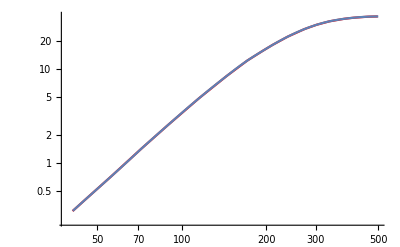

```mathematica
ALVevenRateFit=Interpolation[ALVevenRate,InterpolationOrder->3];
Show[ListLogLogPlot[ALVevenRate,Joined->True,PlotStyle->Red],LogLogPlot[ALVevenRateFit[x],{x,41,500}]]
```

```mathematica
NIntegrate[ALVevenRateFit[x],{x,40,50}]
```

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

4.02547

```mathematica
NIntegrate[ALVevenRateFit[x],{x,40,200}]
```

InterpolatingFunction::dmvali: The integration endpoint 40 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

1037.91

EINSTEIN TELESCOPE

## RE-AVERAGING of the ANTENNA PATTERNS for the EINSTEIN TELESCOPE: 1201.3563

### ANTENNA PATTERN FUNCTIONS: √3/2 times L-shaped F_(+,x) and rotated by 2π/3

```mathematica
Fplus1=(√3)/2 Fplus;
Fx1=(√3)/2 Fx;
Fplus2=(√3)/2 FullSimplify[Fplus/.ϕ->(ϕ+ϕ1)];
Fplus3=(√3)/2 FullSimplify[Fplus/.ϕ->(ϕ+ϕ2)];
Fx2=(√3)/2 FullSimplify[Fx/.ϕ->(ϕ+ϕ1)];
Fx3=(√3)/2 FullSimplify[Fx/.ϕ->(ϕ+ϕ2)];
Fsq=FullSimplify[Fplus1^2+Fplus2^2+Fplus3^2+Fx1^2+Fx2^2+Fx3^2/.ϕ1->2π/3/.ϕ2->4π/3]
Fsqv2=FullSimplify[Fsq/.Cos[4θ]->(8 Cos[θ]^4-3-4Cos[2θ])/.Cos[2θ]->(2 Cos[θ]^2-1)]
```

9/256 (35+28 Cos[2 θ]+Cos[4 θ])

9/32 (1+6 Cos[θ]^2+Cos[θ]^4)

```mathematica
√(Fsqv2/.θ->0)
(√(Fsqv2/.θ->π/2))/(√(Fsqv2/.θ->0))
```

3/2

1/(2 √2)

```mathematica
Fsqv2Av=√(Integrate[Fsqv2 Sin[θ],{θ,0,π}]/2)
```

3/(√10)

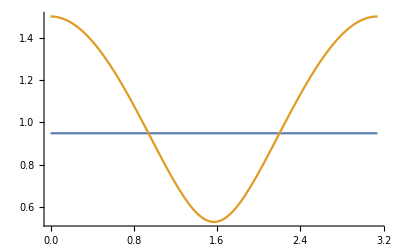

```mathematica
Plot[{Fsqv2Av,√Fsqv2},{θ,0,π}]
```

```mathematica
Minimize[√Fsqv2,θ]
Maximize[√Fsqv2,θ]
```

{3/(4 √2),{θ→π/2}}

{3/2,{θ→0}}

```mathematica
(3./(4 √2))/Fsqv2Av
Fsqv2Av/1.5
```

0.559017

0.632456

### QUALITY FACTOR, ITS NORM-SQUARE and RMS AVERAGE

```mathematica
trigRepl={Sin[2 (ϕ+ϕ1)]->Sin[2ϕ]Cos[2ϕ1]+Cos[2ϕ]Sin[2ϕ1],Sin[2 (ϕ+ϕ2)]->Sin[2ϕ]Cos[2ϕ2]+Cos[2ϕ]Sin[2ϕ2],
Cos[2 (ϕ+ϕ1)]->Cos[2ϕ]Cos[2ϕ1]-Sin[2ϕ]Sin[2ϕ1],Cos[2 (ϕ+ϕ2)]->Cos[2ϕ]Cos[2ϕ2]-Sin[2ϕ]Sin[2ϕ2]};
```

```mathematica
FplusSqSum=Fplus1^2+Fplus2^2+Fplus3^2/.trigRepl/.ϕ1->2π/3/.ϕ2->4π/3//Simplify
FxSqSum=Fx1^2+Fx2^2+Fx3^2/.trigRepl/.ϕ1->2π/3/.ϕ2->4π/3//Simplify
```

(9 (70+56 Cos[2 θ]+2 Cos[4 θ]-4 Cos[2 (θ-2 ψ)]+Cos[4 (θ-ψ)]+6 Cos[4 ψ]+Cos[4 (θ+ψ)]-4 Cos[2 (θ+2 ψ)]))/1024

-(9 (-70-56 Cos[2 θ]-2 Cos[4 θ]-4 Cos[2 (θ-2 ψ)]+Cos[4 (θ-ψ)]+6 Cos[4 ψ]+Cos[4 (θ+ψ)]-4 Cos[2 (θ+2 ψ)]))/1024

```mathematica
FplusSqSumInt=1/(8π)Integrate[(FplusSqSum)Sin[θ]Sin[ι],{θ,0,π},{ψ,0,2π},{ι,0,π}]
FxSqSumInt=1/(8π)Integrate[(FxSqSum)Sin[θ]Sin[ι],{θ,0,π},{ψ,0,2π},{ι,0,π}]
QnormSq=1/2 Integrate[(FplusSqSumInt((1+Cos[i]^2)/2)^2+FxSqSumInt Cos[i]^2)Sin[i],{i,0,-Pi,Pi}]
```

9/20

9/20

9/25

## EINSTEIN TELESCOPE SOURCE STRAIN and RMS-AVERAGED SNR

```mathematica
HET[f_,D_]=Block[{G=6.67*10^-11,c=clight},√QnormSq A c/D(G Mc/c^3)^(5/6)f^(-7/6)]
```

1703.87/(D f^(7/6))

```mathematica
SNRETB[fi_,ff_,D_]:=(NIntegrate[4 HET[f,D]^2/(Snoise[[2]][f])^2,{f,fi,ff}])^(1/2)
SNRETC[fi_,ff_,D_]:=(NIntegrate[4 HET[f,D]^2/(Snoise[[3]][f])^2,{f,fi,ff}])^(1/2)
```

## COSMOLOGICAL REDSHIFT COMPUTATION

```mathematica
(* This data uses 2010 values *)
Clear[z]
RedshiftData=Sort[Import["Redshift.csv","Data"]];
redshift=Interpolation[RedshiftData];
```

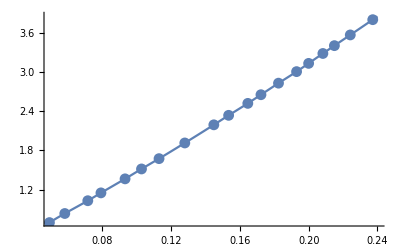

```mathematica
Show[Plot[redshift[z],{z,0.05,0.24}],ListPlot[RedshiftData]]
```

```mathematica
(* Planck 2015 DATA with asro-ph/9905116*)
Pc2LY=3.26156;
GpcScales={1,0.4,0.2,0.1};
ΩΛ=0.6911;
Ωm=0.3089;
Ωk=1-ΩΛ-Ωm;
Ωr= 9.2364 10^-5;
H0=67.74;
h=H0/100;
Ee[z_]=√(Ωr(1+z)^4+Ωm(1+z)^3+Ωk(1+z)^2+ΩΛ);
dC[z_]:=(clight/10^5)/h NIntegrate[1/Ee[zp],{zp,0,z}];
dM[z_]:=dC[z];
dL[z_]:=(1+z)dM[z];
```

```mathematica
Zs=Table[FindRoot[dL[z0]-1000*GpcScales[[i]],{z0,.2}],{i,1,Length[GpcScales]}]//Quiet
Z1Gpc=Zs[[1,1,2]]
Z400Mpc=Zs[[2,1,2]]
Z200Mpc=Zs[[3,1,2]]
Z100Mpc=Zs[[4,1,2]]
{dL[Z1Gpc],dL[Z400Mpc],dL[Z200Mpc],dL[Z100Mpc]}
```

{{z0→0.197981},{z0→0.0850057},{z0→0.0437464},{z0→0.0222204}}

0.197981

0.0850057

0.0437464

0.0222204

{1000.,400.,200.,100.}

```mathematica
fISCOshifted=Reverse[GWfreqIsco/(1+{Z1Gpc,Z400Mpc,Z200Mpc,Z100Mpc})]
```

{1536.82,1505.12,1447.89,1311.34}

## ET-B, ET-C PLOT with SOURCES

### LEGEND

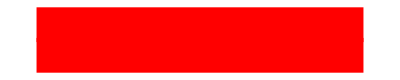
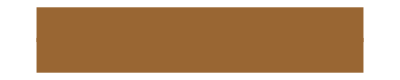
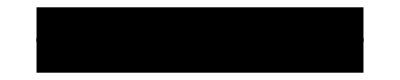

```mathematica
col={Red,Brown,Black};
col2={Blue,Darker[Green],Gray};
legmarkers1=MapThread[Graphics[{#1,AbsoluteThickness[3],Line[{{-1,0},{1,0}}],#2}]&,{col,{Rectangle[{-1,-0.1},{1,0.1}],Rectangle[{-1,-0.1},{1,0.1}],Rectangle[{-1,-0.1},{1,0.1}]}}]
```

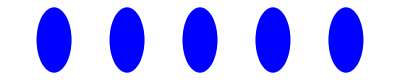
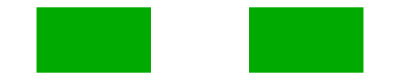
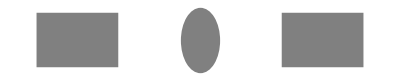

```mathematica
legmarkers2=MapThread[Graphics[{#1,AbsoluteThickness[3],#2}]&,{col2,{{Disk[{1/3,0},0.08],Disk[{0,0},0.08],Disk[{-1/3,0},0.08],Disk[{-2/3,0},0.08],Disk[{2/3,0},0.08]},{Rectangle[{-1,-0.1},{-.3,0.1}],Rectangle[{0.3,-0.1},{1,0.1}]},{Rectangle[{-1,-0.1},{-.5,0.1}],Disk[{0.0,0},0.12],Rectangle[{0.5,-0.1},{1,0.1}]}}}]
```

```mathematica
legmarkers=Flatten[{legmarkers1,legmarkers2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### THE PLOT

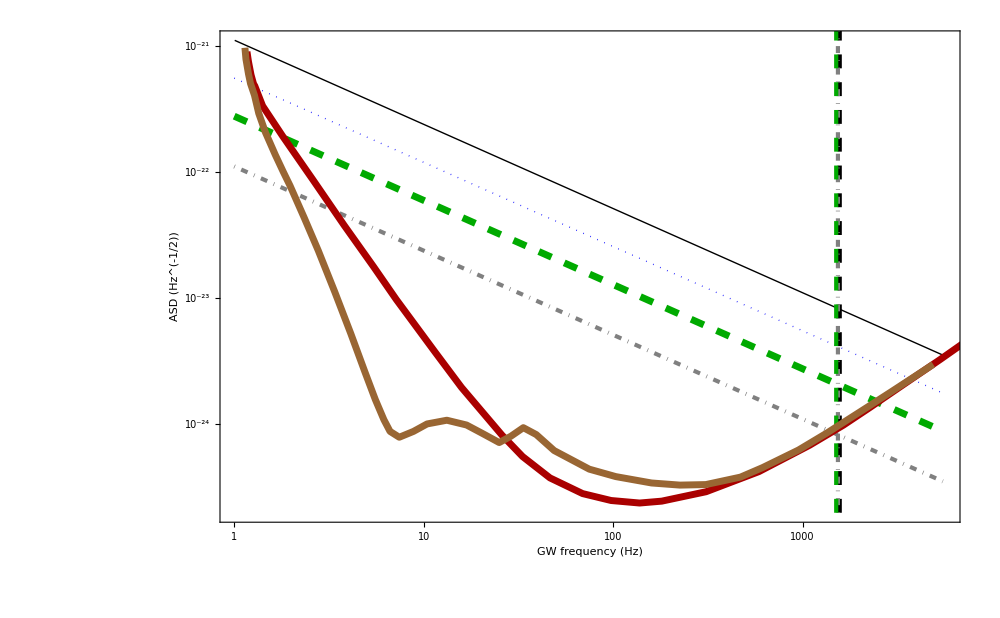

```mathematica
ASDPlots=Show[LogLogPlot[{2 √f HET[f,100Mpc],2 √f HET[f,200Mpc],2 √f HET[f,400Mpc],2 √f HET[f,1000Mpc]},{f,1,5500},PlotRange->{{1,5700},{2 10^-25,1.1 10^-21}},PlotStyle->{{Black,Thick},{Blue,Dotted,Thick},{Darker[Green],Thickness[0.005],Dashing[0.01]},{Gray,Thickness[0.003],DotDashed}}],
Graphics[{Black,Thickness[0.003],Dashing[0.01],Line[{{Log[GWfreqIsco],Log[2 10^-25]},{Log[GWfreqIsco],Log[3 10^-21]}}]}],
Graphics[{Gray,Thickness[0.003],DotDashed,Line[{{Log[fISCOshifted[[1]]],Log[2 10^-25]},{Log[fISCOshifted[[1]]],Log[3 10^-21]}}]}],
Graphics[{Darker[Green],Thickness[0.003],Dashing[0.01],Line[{{Log[fISCOshifted[[2]]],Log[2 10^-25]},{Log[fISCOshifted[[2]]],Log[3 10^-21]}}]}],
ListLogLogPlot[{ETBData,ETCData},Joined->True,PlotStyle->{{Thickness[0.005],Darker[Red]},{Thickness[0.005],Brown}},AxesLabel->{"GW freq.",None}],ImageSize->1000,Frame->True,
FrameStyle->Directive[Black,24,AbsoluteThickness[3]],FrameLabel->{Style["GW frequency (Hz)",24],Style["ASD (Hz^(-1/2))",24]},
GridLines->{{Log[10],Log[5],Log[50],Log[100],Log[500],Log[2],Log[5000]},{Log[10^-24],Log[10^-23],Log[10^-22]}},
FrameTicks->{{{{Log[10^-21],"10^-21"},{Log[10^-22],"10^-22"},{Log[10^-23],"10^-23"},{Log[ 10^-24],"10^-24"}(*,{Log[5 10^-23],"5x10^-23"}*)},None},{{{Log[2],"2"},{Log[5],"5"},{Log[10],"10"},{Log[50],"50"},{Log[100],"100"},{Log[500],"500"},{Log[5000],"5000"},(*{Log[1000],"1000"},*){Log[GWfreqIsco],"f_ISCO"}},None}},FrameTicksStyle->24,
Epilog->Inset[Framed[Column[{
PointLegend[{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic},{Style["ET-B",TextSize],Style["ET-C",TextSize],Style["BNS at 100 Mpc",TextSize],Style["BNS at 200 Mpc",TextSize],Style["BNS at 400 Mpc",TextSize],Style["BNS at 1000 Mpc",TextSize]},LegendMarkers->legmarkers,LegendMarkerSize->{30,10}]}],(*FrameStyle->Directive[Black,AbsoluteThickness[5]],*)RoundingRadius->5,Background->White],Scaled[{0.87,0.84}]]]
(*Export["Figures/ET_strains.pdf",ASDPlots]*)
```

## REDSHIFT CORRECTION to STRAIN, τ_insp and SNR

```mathematica
zs=Reverse[{Z1Gpc,Z400Mpc,Z200Mpc,Z100Mpc}]
```

{0.0222204,0.0437464,0.0850057,0.197981}

```mathematica
HETrs[f_,D_,z_]=Block[{G=6.67*10^-11,c=clight},√QnormSq A c/D(1+z)^(-1/6)(G Mc/c^3)^(5/6)f^(-7/6)]
```

1703.87/(D f^(7/6) (1+z)^(1/6))

```mathematica
SNRETBrs[fi_,ff_,D_,z_]:=(NIntegrate[4 HETrs[f,D,z]^2/(Snoise[[2]][f])^2,{f,fi,ff}])^(1/2)
SNRETCrs[fi_,ff_,D_,z_]:=(NIntegrate[4 HETrs[f,D,z]^2/(Snoise[[3]][f])^2,{f,fi,ff}])^(1/2)
```

## ET PLOTS with REDSHIFTED SOURCES

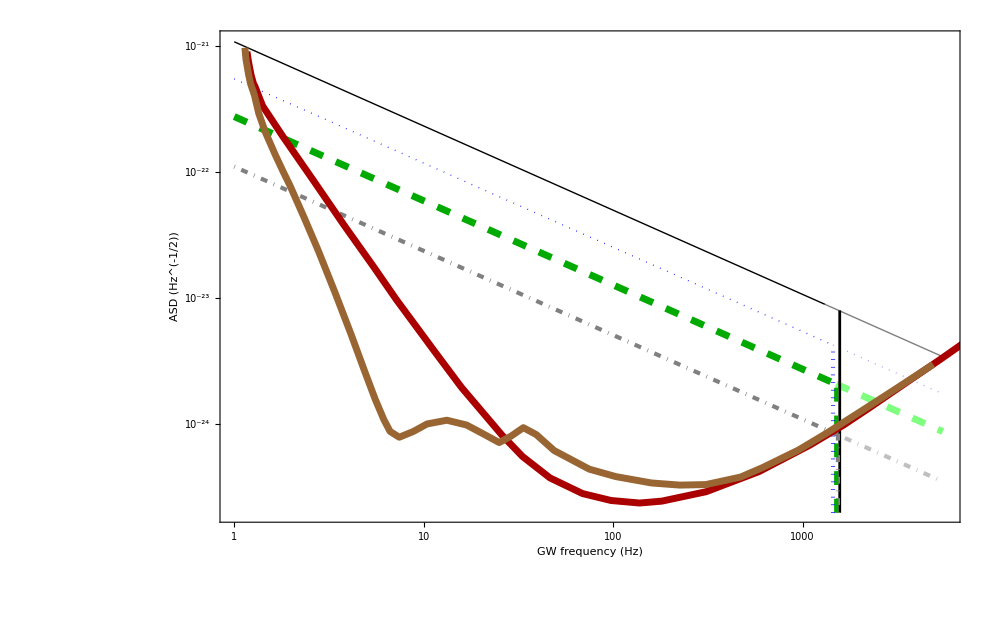

```mathematica
opac=0.5;
ASDPlotsRS=Show[LogLogPlot[{2 √f HETrs[f,100Mpc,zs[[4]]]},{f,1,fISCOshifted[[4]]},PlotRange->{{1,5700},{2 10^-25,1.1 10^-21}},PlotStyle->{Black,Thick}],
LogLogPlot[2 √f HETrs[f,200Mpc,zs[[3]]],{f,1,fISCOshifted[[3]]},PlotStyle->{Blue,Dotted,Thick}],
LogLogPlot[2 √f HETrs[f,400Mpc,zs[[2]]],{f,1,fISCOshifted[[2]]},PlotStyle->{Darker[Green],Thickness[0.005],Dashing[0.01]}],
LogLogPlot[2 √f HETrs[f,1000Mpc,zs[[1]]],{f,1,fISCOshifted[[1]]},PlotStyle->{Gray,Thickness[0.003],DotDashed}],
LogLogPlot[2 √f HETrs[f,100Mpc,zs[[4]]],{f,fISCOshifted[[4]],5500},PlotStyle->{Black,Opacity[opac],Thick}],
LogLogPlot[2 √f HETrs[f,200Mpc,zs[[3]]],{f,fISCOshifted[[3]],5500},PlotStyle->{Blue,Dotted,Opacity[opac],Thick}],
LogLogPlot[2 √f HETrs[f,400Mpc,zs[[2]]],{f,fISCOshifted[[2]],5500},PlotStyle->{Green,Dashing[0.01],Opacity[opac],Thickness[0.005]}],
LogLogPlot[2 √f HETrs[f,1000Mpc,zs[[1]]],{f,fISCOshifted[[1]],5500},PlotStyle->{Gray,Opacity[opac],Thickness[0.003],DotDashed}],
Graphics[{Black,Thickness[0.002],Line[{{Log[GWfreqIsco],Log[2 10^-25]},{Log[GWfreqIsco],Log[ 8 10^-24]}}]}],
Graphics[{Gray,Thickness[0.003],DotDashed,Line[{{Log[fISCOshifted[[1]]],Log[2 10^-25]},{Log[fISCOshifted[[1]]],Log[0.9 10^-24]}}]}],
Graphics[{Darker[Green],Thickness[0.003],Dashing[0.01],Line[{{Log[fISCOshifted[[2]]],Log[2 10^-25]},{Log[fISCOshifted[[2]]],Log[2 10^-24]}}]}],
Graphics[{Blue,Thickness[0.003],Dotted,Line[{{Log[fISCOshifted[[3]]],Log[2 10^-25]},{Log[fISCOshifted[[3]]],Log[4.2 10^-24]}}]}],
ListLogLogPlot[{ETBData,ETCData},Joined->True,PlotStyle->{{Thickness[0.005],Darker[Red]},{Thickness[0.005],Brown}},AxesLabel->{"GW freq.",None}],ImageSize->1000,Frame->True,
FrameStyle->Directive[Black,24,AbsoluteThickness[3]],FrameLabel->{Style["GW frequency (Hz)",24],Style["ASD (Hz^(-1/2))",24]},
GridLines->{{Log[10],Log[5],Log[50],Log[100],Log[500],Log[2],Log[5000]},{Log[10^-24],Log[10^-23],Log[10^-22]}},
FrameTicks->{{{{Log[10^-21],"10^-21"},{Log[10^-22],"10^-22"},{Log[10^-23],"10^-23"},{Log[ 10^-24],"10^-24"}(*,{Log[5 10^-23],"5x10^-23"}*)},None},{{{Log[2],"2"},{Log[5],"5"},{Log[10],"10"},{Log[50],"50"},{Log[100],"100"},{Log[500],"500"},{Log[5000],"5000"},(*{Log[1000],"1000"},*){Log[GWfreqIsco],"f_ISCO"}},None}},FrameTicksStyle->24,
Epilog->Inset[Framed[Column[{
PointLegend[{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic},{Style["ET-B",TextSize],Style["ET-C",TextSize],Style["BNS at 100 Mpc",TextSize],Style["BNS at 200 Mpc",TextSize],Style["BNS at 400 Mpc",TextSize],Style["BNS at 1000 Mpc",TextSize]},LegendMarkers->legmarkers,LegendMarkerSize->{30,10}]}],(*FrameStyle->Directive[Black,AbsoluteThickness[5]],*)RoundingRadius->5,Background->White],Scaled[{0.87,0.84}]]]
(*Export["Figures/ET_strains_redshifted.pdf",ASDPlotsRS]*)
```

## ET-B, ET-C Advance Warning Times and SNRs 3.5PN calculation uses x -> x (1+z)^(2/3) and Θ -> (1+z)^-1Θ

### ET-B, ET-C entry frequencies f_0 for 4 sources

```mathematica
ETf0RootFinderRS[D_,fB_,fC_,z_]:={2 √fB HETrs[fB,D,z]-Snoise[[2]][fB],2 √fC HETrs[fC,D,z]-Snoise[[3]][fC]}
```

```mathematica
f0ETrs={FindRoot[ETf0RootFinderRS[100Mpc,f1,f2,zs[[1]]],{{f1,1},{f2,1}}][[All,2]],
FindRoot[ETf0RootFinderRS[200Mpc,f1,f2,zs[[2]]],{{f1,1},{f2,1}}][[All,2]],FindRoot[ETf0RootFinderRS[400Mpc,f1,f2,zs[[3]]],{{f1,1},{f2,1}}][[All,2]],
FindRoot[ETf0RootFinderRS[1000Mpc,f1,f2,zs[[4]]],{{f1,1},{f2,1}}][[All,2]]}//Quiet
```

{{1.15173,1.13483},{1.30064,1.2336},{1.92124,1.45212},{3.61223,2.10482}}

```mathematica
f0B=f0ETrs[[All,1]]
f0C=f0ETrs[[All,2]]
```

{1.15173,1.30064,1.92124,3.61223}

{1.13483,1.2336,1.45212,2.10482}

### D = 100 Mpc

```mathematica
(* ET-B *)
DL=100Mpc;
j=1;
fbar=6.7237;
SNRETBrs[f0B[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/60," minutes(3.5PN), "]
ρtot=SNRETBrs[f0B[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]

(* ET-C *)
fbar=3.26919;
SNRETCrs[f0C[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/3600," hours(3.5PN), "]
ρtot=SNRETCrs[f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

14.9999

τ_insp = 2818.29(3.5PN), 2818.61(2PN) 2786.76(0 PN)  seconds

τ_insp = 46.9715 minutes(3.5PN),

ρ_tot = 305.99

15.

τ_insp = 19212.3(3.5PN), 19213.(2PN) 19064.(0 PN)  seconds

τ_insp = 5.33676 hours(3.5PN),

ρ_tot = 365.544

### D = 200 Mpc

```mathematica
(* ET-B *)
DL=200Mpc;
j=2;
fbar=11.21037;
SNRETBrs[f0B[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/60," minutes(3.5PN), "]
ρtot=SNRETBrs[f0B[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]

(* ET-C *)
fbar=4.10277;
SNRETCrs[f0C[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/3600," hours(3.5PN), "]
ρtot=SNRETCrs[f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

14.9999

τ_insp = 698.595(3.5PN), 698.786(2PN) 688.628(0 PN)  seconds

τ_insp = 11.6433 minutes(3.5PN),

ρ_tot = 152.463

14.9999

τ_insp = 10137.7(3.5PN), 10138.3(2PN) 10048.4(0 PN)  seconds

τ_insp = 2.81603 hours(3.5PN),

ρ_tot = 182.137

### D = 400 Mpc

```mathematica
(* ET-B *)
DL=400Mpc;
j=3;
fbar=18.2234;
SNRETBrs[f0B[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/60," minutes(3.5PN), "]
ρtot=SNRETBrs[f0B[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]

(* ET-C *)
fbar=5.06068;
SNRETCrs[f0C[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/3600," hours(3.5PN), "]
ρtot=SNRETCrs[f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

14.9993

τ_insp = 179.831(3.5PN), 179.946(2PN) 176.698(0 PN)  seconds

τ_insp = 2.99719 minutes(3.5PN),

ρ_tot = 75.7376

14.9999

τ_insp = 5437.36(3.5PN), 5437.79(2PN) 5382.93(0 PN)  seconds

τ_insp = 1.51038 hours(3.5PN),

ρ_tot = 90.4805

### D = 1000 Mpc

```mathematica
(* ET-B *)
DL=1000Mpc;
j=4;
fbar=41.3537;
SNRETBrs[f0B[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
ρtot=SNRETBrs[f0B[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]

(* ET-C *)
fbar=6.75534;
SNRETCrs[f0C[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])M], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/3600," hours(3.5PN), "]
ρtot=SNRETCrs[f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

14.9996

τ_insp = 17.1969(3.5PN), 17.2451(2PN) 16.8464(0 PN)  seconds

ρ_tot = 29.7927

14.9996

τ_insp = 2138.48(3.5PN), 2138.8(2PN) 2112.61(0 PN)  seconds

τ_insp = 0.594022 hours(3.5PN),

ρ_tot = 35.5958

```mathematica
{2818,698.6,179.8}/60.
```

{46.9667,11.6433,2.99667}

```mathematica
{19212,10318,5437}/3600.
2138/60.
```

{5.33667,2.86611,1.51028}

35.6333

## MAJOR PLOT SUMMARIZING MAIN RESULTS

```mathematica
DistData={50,100,200,400,1000};
ALVtimes={113.1,33.08,4.948};
ALVSNR={84.2,42.1,21};
ETtimes={{2818,698.6,179.8,17.2},{19212,10138,5437,2138}};
ETSNR={{306,152.4,75.74,29.79},{365.4,182.1,90.48,35.6}};
```

```mathematica
ALVSNRdata=Table[{DistData[[i]],ALVSNR[[i]]},{i,1,Length[ALVtimes]}];
ALVtimedata=Table[{DistData[[i]],ALVtimes[[i]]},{i,1,Length[ALVtimes]}];
ETBSNRdata=Table[{DistData[[i+1]],ETSNR[[1,i]]},{i,1,Length[ETtimes[[1]]]}];
ETBtimesdata=Table[{DistData[[i+1]],ETtimes[[1,i]]},{i,1,Length[ETtimes[[1]]]}];
ETCSNRdata=Table[{DistData[[i+1]],ETSNR[[2,i]]},{i,1,Length[ETtimes[[1]]]}];
ETCtimesdata=Table[{DistData[[i+1]],ETtimes[[2,i]]},{i,1,Length[ETtimes[[1]]]}];
```

### LEGEND

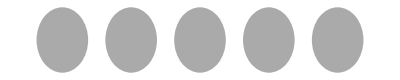
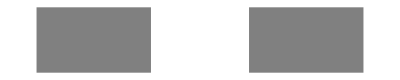
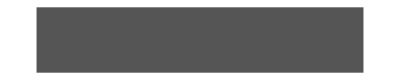
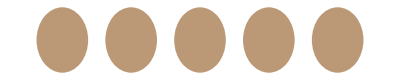
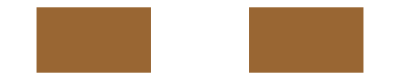
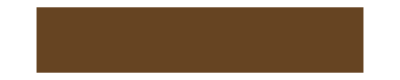

```mathematica
color1=Gray;
color2=Brown;
col1={Lighter[color1],color1,Darker[color1]};
col2={Lighter[color2],color2,Darker[color2]};
diskrad=0.125;
legmarkers1=MapThread[Graphics[{#1,AbsoluteThickness[3],#2}]&,{col1,{{Disk[{1/3,0},diskrad],Disk[{0,0},diskrad],Disk[{-1/3,0},diskrad],Disk[{-2/3,0},diskrad],Disk[{2/3,0},diskrad]},{Rectangle[{-1,-diskrad},{-.3,diskrad}],Rectangle[{0.3,-diskrad},{1,diskrad}]},{Rectangle[{-1,-diskrad},{1,diskrad}]}}}];
legmarkers2=MapThread[Graphics[{#1,AbsoluteThickness[3],#2}]&,{col2,{{Disk[{1/3,0},diskrad],Disk[{0,0},diskrad],Disk[{-1/3,0},diskrad],Disk[{-2/3,0},diskrad],Disk[{2/3,0},diskrad]},{Rectangle[{-1,-diskrad},{-.3,diskrad}],Rectangle[{0.3,-diskrad},{1,diskrad}]},{Rectangle[{-1,-diskrad},{1,diskrad}]}}}];
legmarkers=Flatten[{legmarkers1,legmarkers2}]
```

### THE PLOT

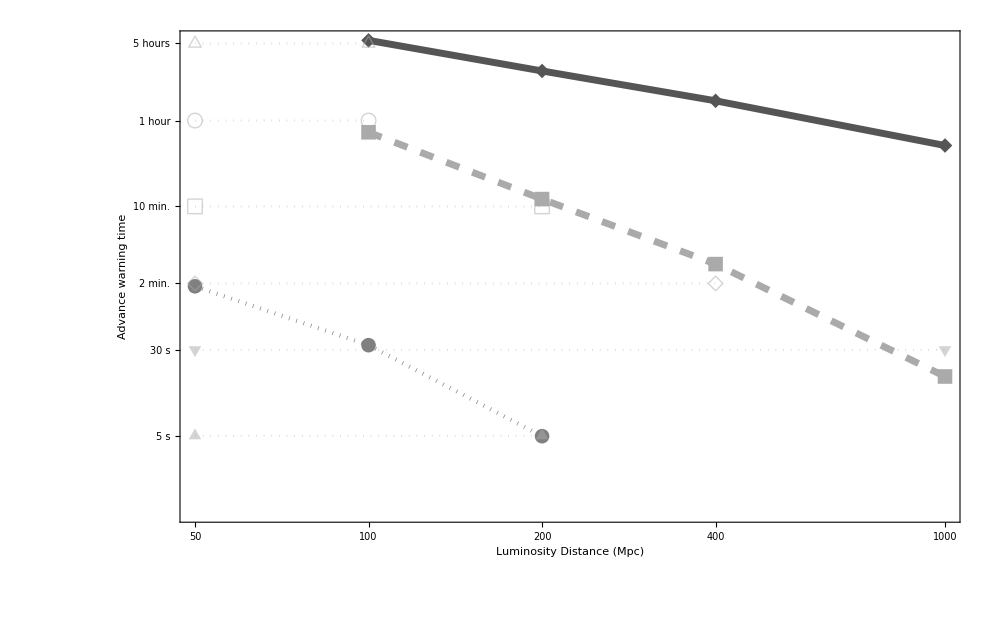

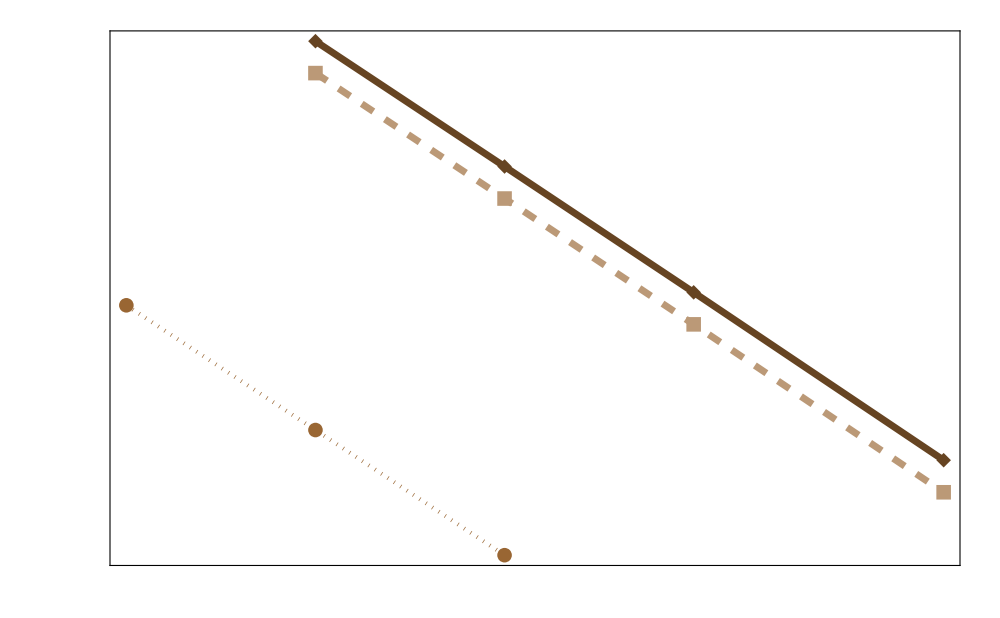
-Graphics--Graphics-

```mathematica
grid1={{50,5},{200,5}};
grid2={{50,30},{1000,30}};
grid3={{50,3600},{100,3600}};
grid4={{50,600},{200,600}};
grid5={{50,120},{400,120}};
grid6={{50,18000},{100,18000}};

TextSize=20;
plot1=ListPlot[Log[{ALVtimedata,ETBtimesdata,ETCtimesdata,grid1,grid2,grid3,grid4,grid5,grid6}],PlotStyle->{{color1,Dotted,Thickness[0.003]},{Lighter[color1],Dashing[0.01],Thickness[0.005]},{Darker[color1],Thickness[0.005]},{Lighter[color1],Dotted,Opacity[opac]},{Lighter[color1],Dotted,Opacity[opac]},{Lighter[color1],Dotted,Opacity[opac]},{Lighter[color1],Dotted,Opacity[opac]},{Lighter[color1],Dotted,Opacity[opac]},{Lighter[color1],Dotted,Opacity[opac]}},
ImagePadding->{{130,100},{30,5}},
Frame->{True,True,True,False},Joined->True,PlotMarkers->{Automatic,15},FrameStyle->{Directive[Black,24,AbsoluteThickness[3]],Directive[color1,24,AbsoluteThickness[3]],Directive[Black,24,AbsoluteThickness[3]],Automatic},FrameLabel->{"Luminosity Distance (Mpc)","Advance warning time"},FrameStyle->Directive[Black,24,AbsoluteThickness[3]],BaseStyle->{FontSize->TextSize},
GridLines->{{Log[50],Log[100],Log[200],Log[400],Log[1000]},None},
FrameTicks->{{{{Log[600],"10 min."},{Log[120],"2 min."},{Log[30],"30 s"},{Log[18000],"5 hours"},{Log[5],"5 s"},{Log[3600],"1 hour"}},None},{{{Log[100],"100"},{Log[200],"200"},{Log[400],"400"},{Log[50],"50"},{Log[1000],"1000"}},None}},
ImageSize->1000,Epilog->Inset[Framed[Column[{
PointLegend[{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic},{Style["ALV",TextSize],Style["ET-B",TextSize],Style["ET-C",TextSize],Style["ALV",TextSize],Style["ET-B",TextSize],Style["ET-C",TextSize]},LegendMarkers->legmarkers,LegendMarkerSize->{30,20}]}],RoundingRadius->5,Background->White],Scaled[{0.1,0.75}]]]

plot2=ListPlot[Log[{ALVSNRdata,ETBSNRdata,ETCSNRdata}],PlotStyle->{{color2,Dotted,Thickness[0.003]},{Lighter[color2],Dashing[0.01],Thickness[0.005]},{Thickness[0.005],Darker[color2]}},ImagePadding->{{130,100},{30,5}},
Axes->False,Frame->{False,False,False,True},Joined->True,PlotMarkers->{Automatic,15},FrameTicks->{None,None,None,{{Log[100],"100"},{Log[200],"200"},{Log[50],"50"},{Log[100],"100"},{Log[350],"350"},{Log[20],"20"}}},FrameStyle->{Automatic,Automatic,Automatic,Directive[color2,24,AbsoluteThickness[3]]},
FrameLabel->{{None,"SNR"},{None,None}},ImageSize->1000];
MainResults=Overlay[{plot1,plot2}]
(*Export["Figures/Main_results.pdf",MainResults]*)
```

## ET-B, ET-C Horizon Distance Computation for T_AW= 1 hour

### ET-B

```mathematica
dtest=86.87;
ztest=FindRoot[dL[z0]-dtest,{z0,.2}][[1,2]]//Quiet
ftest=FindRoot[Tinsp0PN[f1,(1+ztest)Mc] -3600,{f1,20}][[1,2]]
fintest=FindRoot[2 √fC HETrs[fC,dtest Mpc,ztest]-Snoise[[2]][fC],{fC,1}][[1,2]]//Quiet
SNRETBrs[fintest,ftest,dtest Mpc,ztest]
(dtest/1000.)^3{1540-1220,1540,1540+3200}
(dtest/1000.)^3{1220,3200}
SNRETCrs[fintest,GWfreqIsco/(1+ztest),dtest Mpc,ztest]
Print["Time it takes to accumulate ρ=15:\t", (Tinsp0PN[fintest,(1+ztest)Mc] -Tinsp0PN[ftest,(1+ztest)Mc] )/3600/24, " days"]
```

0.0193443

6.11888

1.12709

15.0106

{0.209778,1.00956,3.10733}

{0.799778,2.09778}

420.993

Time it takes to accumulate ρ=15:	3.75169 days

### ET-C

```mathematica
dtest=613;
ztest=FindRoot[dL[z0]-dtest,{z0,.2}][[1,2]]//Quiet
ftest=FindRoot[Tinsp0PN[f1,(1+ztest)Mc] -3600,{f1,20}][[1,2]]
fintest=FindRoot[2 √fC HETrs[fC,dtest Mpc,ztest]-Snoise[[3]][fC],{fC,1}][[1,2]]//Quiet
SNRETCrs[fintest,ftest,dtest Mpc,ztest]
Print["Time it takes to accumulate ρ=15:\t", (Tinsp0PN[fintest,(1+ztest)Mc] -Tinsp0PN[ftest,(1+ztest)Mc] )/3600/24, " days"]
```

0.12674

5.74755

1.70599

15.0087

Time it takes to accumulate ρ=15:	1.02118 days

```mathematica
(* EVENT RATES within horizon distance *)
```

```mathematica
(dtest/1000.)^3{1540-1220,1540,1540+3200}
(dtest/1000.)^3{1220,3200}
```

{73.7108,354.733,1091.84}

{281.023,737.108}

```mathematica
(* Total SNR at horizon distance *)
SNRETCrs[fintest,GWfreqIsco/(1+ztest),dtest Mpc,ztest]
```

58.6692

## LISA COMPUTATIONS

```mathematica
LisaData=Sort[Import["LISA.csv","Data"]];
LisaASD=Interpolation[LisaData,InterpolationOrder->1]
```

InterpolatingFunction[{{0.000317598, 0.0345281}}, <>]

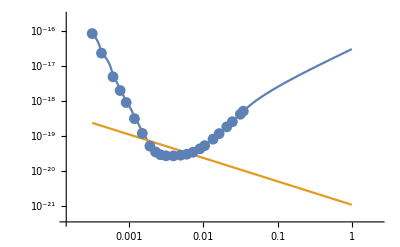

```mathematica
Show[LogLogPlot[{LisaASD[f],2 √f HET[f,100Mpc]},{f,LisaData[[1,1]],1}],ListLogLogPlot[LisaData]]
```

```mathematica
SNRLisa[fi_,ff_,D_]:=(NIntegrate[4 HET[f,D]^2/(LisaASD[f])^2,{f,fi,ff}])^(1/2)
```

```mathematica
LisaData[[1,1]]
```

0.000317598

BH-NS Binary at ET

## ET-B, ET-C Advance Warning Times and SNRs Use M = (1.4+5)M_sun

```mathematica
Clear[M]
M2=5;
```

```mathematica
HETrsBHNS[m2_,f_,D_,z_]=Block[{m1=1.4Msun,G=6.67*10^-11,c=clight},√QnormSq A c/D(1+z)^(-1/6)(G (m1 m2)^(3/5)/((m1+m2)^(1/5)c^3))^(5/6)f^(-7/6)]
```

(1.35942×10^-7 (m2^(3/5)/((2.7846×10^30+m2)^(1/5)))^(5/6))/(D f^(7/6) (1+z)^(1/6))

```mathematica
SNRETBrsBHNS[m2_,fi_,ff_,D_,z_]:=(NIntegrate[4 HETrsBHNS[m2,f,D,z]^2/(Snoise[[2]][f])^2,{f,fi,ff}])^(1/2)
SNRETCrsBHNS[m2_,fi_,ff_,D_,z_]:=(NIntegrate[4 HETrsBHNS[m2,f,D,z]^2/(Snoise[[3]][f])^2,{f,fi,ff}])^(1/2)
```

```mathematica
(*Check*)
(m1 m2)^(3/5)/(m1+m2)^(1/5)/.m2->m1/.m1->1.4Msun
```

2.42414×10^30

```mathematica
Mc/.M->2.8Msun
```

2.42414×10^30

```mathematica
Q=5/1.4;
fact=√(q2/q1)((1+q1)/(1+q2))^(1/6)/.q1->1/.q2->Q
```

1.64658

## PLOTS

### LEGEND

```mathematica
col={Red,Brown,Black};
col2={Blue,Darker[Green],Gray};
legmarkers1=MapThread[Graphics[{#1,AbsoluteThickness[3],Line[{{-1,0},{1,0}}],#2}]&,{col,{Rectangle[{-1,-0.1},{1,0.1}],Rectangle[{-1,-0.1},{1,0.1}],Rectangle[{-1,-0.1},{1,0.1}]}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
legmarkers2=MapThread[Graphics[{#1,AbsoluteThickness[3],#2}]&,{col2,{{Disk[{1/3,0},0.08],Disk[{0,0},0.08],Disk[{-1/3,0},0.08],Disk[{-2/3,0},0.08],Disk[{2/3,0},0.08]},{Rectangle[{-1,-0.1},{-.3,0.1}],Rectangle[{0.3,-0.1},{1,0.1}]},{Rectangle[{-1,-0.1},{-.5,0.1}],Disk[{0.0,0},0.12],Rectangle[{0.5,-0.1},{1,0.1}]}}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
legmarkers=Flatten[{legmarkers1,legmarkers2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### The PLOT

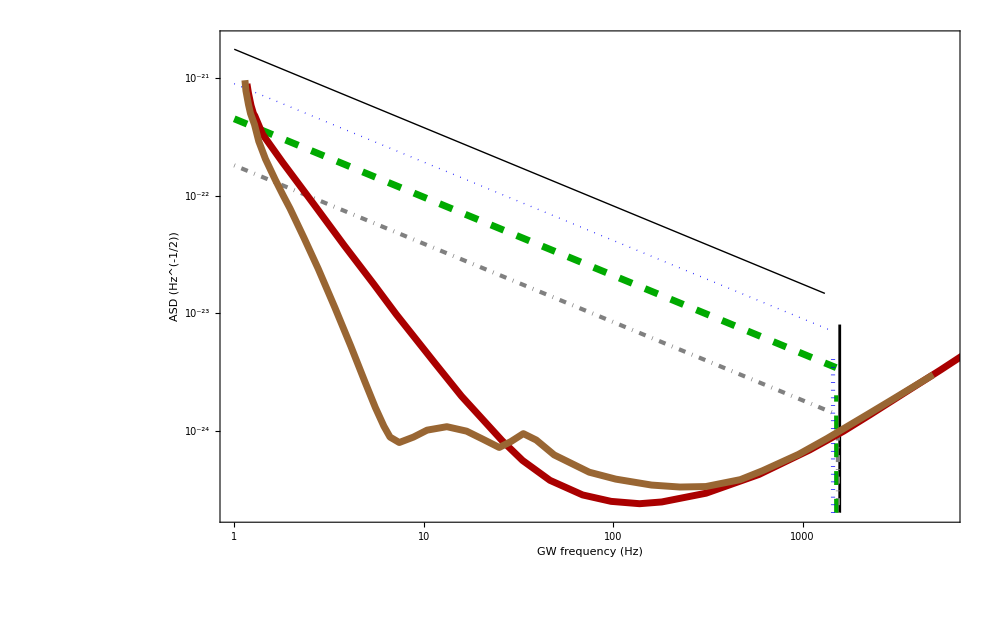

```mathematica
ASDPlotsRS=Show[LogLogPlot[{2 √f HETrsBHNS[M2 Msun,f,100Mpc,zs[[4]]]},{f,1,fISCOshifted[[4]]},PlotRange->{{1,5700},{2 10^-25,2.1 10^-21}},PlotStyle->{Black,Thick}],
LogLogPlot[2 √f HETrsBHNS[M2 Msun,f,200Mpc,zs[[3]]],{f,1,fISCOshifted[[3]]},PlotStyle->{Blue,Dotted,Thick}],
LogLogPlot[2 √f HETrsBHNS[M2 Msun,f,400Mpc,zs[[2]]],{f,1,fISCOshifted[[2]]},PlotStyle->{Darker[Green],Thickness[0.005],Dashing[0.01]}],
LogLogPlot[2 √f HETrsBHNS[M2 Msun,f,1000Mpc,zs[[1]]],{f,1,fISCOshifted[[1]]},PlotStyle->{Gray,Thickness[0.003],DotDashed}],
Graphics[{Black,Thickness[0.002],Line[{{Log[GWfreqIsco],Log[2 10^-25]},{Log[GWfreqIsco],Log[ 8 10^-24]}}]}],
Graphics[{Gray,Thickness[0.003],DotDashed,Line[{{Log[fISCOshifted[[1]]],Log[2 10^-25]},{Log[fISCOshifted[[1]]],Log[0.9 10^-24]}}]}],
Graphics[{Darker[Green],Thickness[0.003],Dashing[0.01],Line[{{Log[fISCOshifted[[2]]],Log[2 10^-25]},{Log[fISCOshifted[[2]]],Log[2 10^-24]}}]}],
Graphics[{Blue,Thickness[0.003],Dotted,Line[{{Log[fISCOshifted[[3]]],Log[2 10^-25]},{Log[fISCOshifted[[3]]],Log[4.2 10^-24]}}]}],
ListLogLogPlot[{ETBData,ETCData},Joined->True,PlotStyle->{{Thickness[0.005],Darker[Red]},{Thickness[0.005],Brown}},AxesLabel->{"GW freq.",None}],ImageSize->1000,Frame->True,
FrameStyle->Directive[Black,24,AbsoluteThickness[3]],FrameLabel->{Style["GW frequency (Hz)",24],Style["ASD (Hz^(-1/2))",24]},
GridLines->{{Log[10],Log[5],Log[50],Log[100],Log[500],Log[2],Log[5000]},{Log[10^-24],Log[10^-23],Log[10^-22]}},
FrameTicks->{{{{Log[10^-21],"10^-21"},{Log[10^-22],"10^-22"},{Log[10^-23],"10^-23"},{Log[ 10^-24],"10^-24"}(*,{Log[5 10^-23],"5x10^-23"}*)},None},{{{Log[2],"2"},{Log[5],"5"},{Log[10],"10"},{Log[50],"50"},{Log[100],"100"},{Log[500],"500"},{Log[5000],"5000"},(*{Log[1000],"1000"},*){Log[GWfreqIsco],"f_ISCO"}},None}},FrameTicksStyle->24,
Epilog->Inset[Framed[Column[{
PointLegend[{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic},{Style["ET-B",TextSize],Style["ET-C",TextSize],Style["BNS at 100 Mpc",TextSize],Style["BNS at 200 Mpc",TextSize],Style["BNS at 400 Mpc",TextSize],Style["BNS at 1000 Mpc",TextSize]},LegendMarkers->legmarkers,LegendMarkerSize->{30,10}]}],(*FrameStyle->Directive[Black,AbsoluteThickness[5]],*)RoundingRadius->5,Background->White],Scaled[{0.87,0.84}]]]
```

## WARNING TIMES

### A-LIGO

```mathematica
ftest=Block[{D=50Mpc,M=(1.4+M2)Msun},FindRoot[2 √fRMS hFDRMS[fRMS,D]-Snoise[[1]][fRMS],{fRMS,10}]][[1,2]]
```

9.28585

```mathematica
fbar=25.35;
Block[{f=fbar,D=50Mpc,M=2.8Msun},(SNRMax[1,ftest,f,D]^2+SNRRMS[1,ftest,f,D]^2+SNRLow[1,ftest,f,D]^2)^(1/2)];
 Print["τ_insp = ",Tinsp0PN[fbar,Mc]/.M->(1.4+M2)Msun," seconds"]
```

τ_insp = 21.1666 seconds

### ET-B, ET-C entry frequencies f_0 for 4 sources

```mathematica
fISCOshifted=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},Reverse[fISCO/(1+{Z1Gpc,Z400Mpc,Z200Mpc,Z100Mpc})]]
```

{672.357,658.491,633.451,573.713}

```mathematica
ETf0RootFinderRS[D_,fB_,fC_,z_]:=Block[{m2=5Msun},{2 √fB fact HETrsBHNS[m2,fB,D,z]-Snoise[[2]][fB],2 √fC fact HETrsBHNS[m2,fC,D,z]-Snoise[[3]][fC]}]
```

```mathematica
f0ETrs={FindRoot[ETf0RootFinderRS[100Mpc,f1,f2,zs[[1]]],{{f1,1},{f2,1}}][[All,2]],
FindRoot[ETf0RootFinderRS[200Mpc,f1,f2,zs[[2]]],{{f1,1},{f2,1}}][[All,2]],FindRoot[ETf0RootFinderRS[400Mpc,f1,f2,zs[[3]]],{{f1,1},{f2,1}}][[All,2]],
FindRoot[ETf0RootFinderRS[1000Mpc,f1,f2,zs[[4]]],{{f1,1},{f2,1}}][[All,2]]}//Quiet
```

{{0.786552,0.975298},{1.09343,1.10489},{1.21166,1.17615},{1.78547,1.42993}}

```mathematica
f0B=f0ETrs[[All,1]]
f0C=f0ETrs[[All,2]]
```

{0.786552,1.09343,1.21166,1.78547}

{0.975298,1.10489,1.17615,1.42993}

### D = 100 Mpc (* Entry frequency set = 1 Hz artificially *)

```mathematica
(* ET-B *)
DL=100Mpc;
j=1;
fbar=4.863;
SNRETBrsBHNS[M2 Msun,1,fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])(1.4+M2)Msun], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc] /.M->((1.4+M2)Msun),"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/60," minutes(3.5PN), "]
ρtot=SNRETBrsBHNS[M2 Msun,1,fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]

(* ET-C *)
fbar=2.7331;
SNRETCrsBHNS[M2 Msun,1,fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])(1.4+M2)Msun], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc]/.M->((1.4+M2)Msun) ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/3600," hours(3.5PN), "]
ρtot=SNRETCrsBHNS[M2 Msun,1,fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

14.9998

τ_insp = 1690.84(3.5PN), 1691.28(2PN) 1667.02(0 PN)  seconds

τ_insp = 28.1807 minutes(3.5PN),

ρ_tot = 503.047

15.0001

τ_insp = 7833.99(3.5PN), 7834.79(2PN) 7749.44(0 PN)  seconds

τ_insp = 2.17611 hours(3.5PN),

ρ_tot = 601.278

### D = 200 Mpc

```mathematica
(* ET-B *)
DL=200Mpc;
j=2;
fbar=7.629;
SNRETBrsBHNS[M2 Msun,f0B[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])(1.4+M2)Msun], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc]/.M->((1.4+M2)Msun) ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/60," minutes(3.5PN), "]
ρtot=SNRETBrsBHNS[M2 Msun,f0B[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]

(* ET-C *)
fbar=3.48135;
SNRETCrsBHNS[M2 Msun,f0C[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])(1.4+M2)Msun], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc]/.M->((1.4+M2)Msun) ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/3600," hours(3.5PN), "]
ρtot=SNRETCrsBHNS[M2 Msun,f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

15.0003

τ_insp = 492.919(3.5PN), 493.194(2PN) 484.567(0 PN)  seconds

τ_insp = 8.21531 minutes(3.5PN),

ρ_tot = 250.624

15.0001

τ_insp = 3974.57(3.5PN), 3975.2(2PN) 3925.91(0 PN)  seconds

τ_insp = 1.10405 hours(3.5PN),

ρ_tot = 299.576

### D = 400 Mpc

```mathematica
(* ET-B *)
DL=400Mpc;
j=3;
fbar=12.745;
SNRETBrsBHNS[M2 Msun,f0B[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])(1.4+M2)Msun], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc]/.M->((1.4+M2)Msun) ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/60," minutes(3.5PN), "]
ρtot=SNRETBrsBHNS[M2 Msun,f0B[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]

(* ET-C *)
fbar=4.357;
SNRETCrsBHNS[M2 Msun,f0C[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])(1.4+M2)Msun], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc]/.M->((1.4+M2)Msun) ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/60," minutes(3.5PN), "]
ρtot=SNRETCrsBHNS[M2 Msun,f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

15.0007

τ_insp = 117.929(3.5PN), 118.09(2PN) 115.602(0 PN)  seconds

τ_insp = 1.96549 minutes(3.5PN),

ρ_tot = 124.478

15.0006

τ_insp = 2051.49(3.5PN), 2051.98(2PN) 2023.2(0 PN)  seconds

τ_insp = 34.1915 minutes(3.5PN),

ρ_tot = 148.802

### D = 1000 Mpc

```mathematica
(* ET-B *)
DL=1000Mpc;
j=4;
fbar=26.43;
SNRETBrsBHNS[M2 Msun,f0B[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])(1.4+M2)Msun], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc]/.M->((1.4+M2)Msun) ,"(0 PN) "," seconds"]
ρtot=SNRETBrsBHNS[M2 Msun,f0B[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]

(* ET-C *)
fbar=5.74775;
SNRETCrsBHNS[M2 Msun,f0C[[j]],fbar,DL,zs[[j]]]
fin=fbar;
Th=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},Θ/(1+zs[[j]])];
xin=Block[{G=6.67*10^-11,M=(6.4Msun),c=clight},(1+zs[[j]])^(2/3)Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];

Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOshifted[[j]],fin,(1+zs[[j]])(1.4+M2)Msun], "(2PN) ", Tinsp0PN[fin,(1+zs[[j]])Mc]/.M->((1.4+M2)Msun) ,"(0 PN) "," seconds"]
Print["τ_insp = ",Tinsp3p5PN/60," minutes(3.5PN), "]
ρtot=SNRETCrsBHNS[M2 Msun,f0C[[j]],fISCOshifted[[j]],DL,zs[[j]]];
Print["ρ_tot = ", ρtot]
```

15.0007

τ_insp = 14.2756(3.5PN), 14.349(2PN) 14.0147(0 PN)  seconds

ρ_tot = 48.9417

15.0006

τ_insp = 832.821(3.5PN), 833.189(2PN) 819.436(0 PN)  seconds

τ_insp = 13.8804 minutes(3.5PN),

ρ_tot = 58.5202

### ET-C Horizon distance computation for T_AW= 1 hour and the corresponding event rate

```mathematica
(* EVENT RATES within horizon distance *)
```

```mathematica
dtest=200
R=3600.*(200/1000)^3
```

200

28.8

## LISA COMPUTATIONS -> NEGLIGIBLE

```mathematica
LisaData=Sort[Import["LISA.csv","Data"]];
LisaASD=Interpolation[LisaData,InterpolationOrder->1]
```

InterpolatingFunction[{{0.000317598, 0.0345281}}, <>]

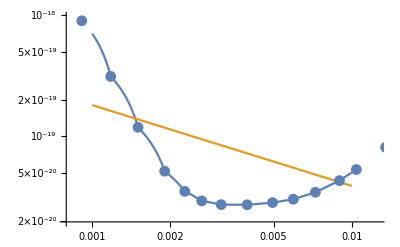

```mathematica
Show[LogLogPlot[{LisaASD[f],2 √f HETrsBHNS[M2 Msun,f,100Mpc,Z100Mpc]},{f,0.001,0.01}],ListLogLogPlot[LisaData]]
```

```mathematica
NIntegrate[4(HETrsBHNS[M2 Msun,f,100Mpc,Z100Mpc]/LisaASD[f])^2,{f,1.5 10^-3,0.009}]^(1/2)
```

3.11174

```mathematica
3600/125.
```

28.8